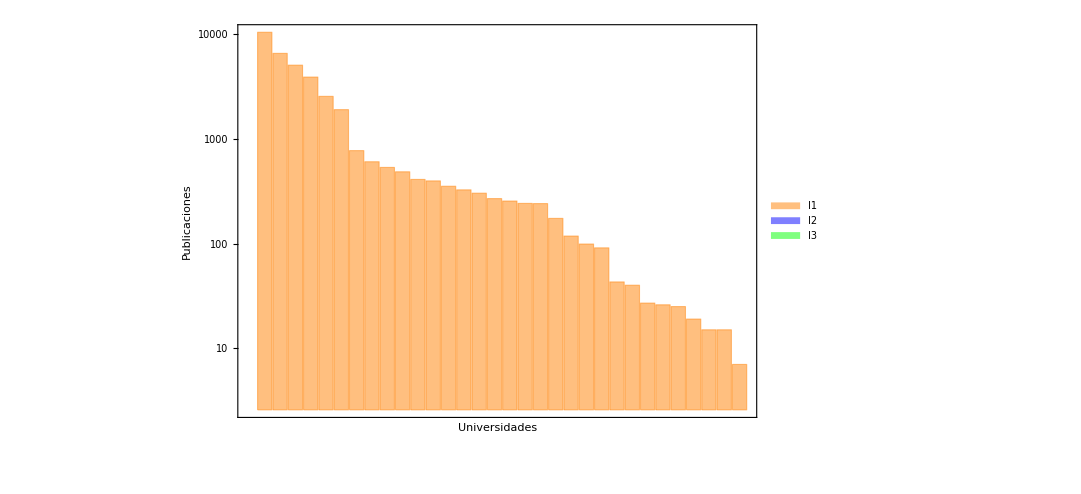

```mathematica
y = "/home/fabianact/ActualTesis/Tesis/ModelosPresentados";
SetDirectory["/home/fabianact/ActualTesis/Tesis/ModelosPresentados/Distribución"];
SetOptions[BarChart,BaseStyle->{FontSize->20}];
data1 = Import[y<>"/Distribución/Colombia.csv"];
Fdata1 = Flatten[data1];

plot=Legended[Show[{{BarChart[{Fdata1},ImageSize->800,  ChartStyle->{Directive[Orange,Opacity[.5]]}, Axes->{False, True}, ScalingFunctions->"Log"]}}, Frame->{{True, None},{True, None}}, FrameLabel->{"Universidades","Publicaciones"}], Placed[SwatchLegend[{Directive[Orange,Opacity[.5]],Directive[Blue,Opacity[.5]],Directive[Green,Opacity[.5]]},{Style["I1",17],Style["I2",17],Style["I3",17]},LegendMargins->{{35,15},{5,5}},LegendFunction->Framed,LabelStyle->(FontFamily->"Helvetica")],{{0.7,0.7},{0,0}}]]
```